```mathematica
Solve[g/(1-g)==r a /(1-a), g]
```

{{g→(a r)/(1-a+a r)}}

```mathematica
f[r_]:=(a r)/(1-a(1- r))
```

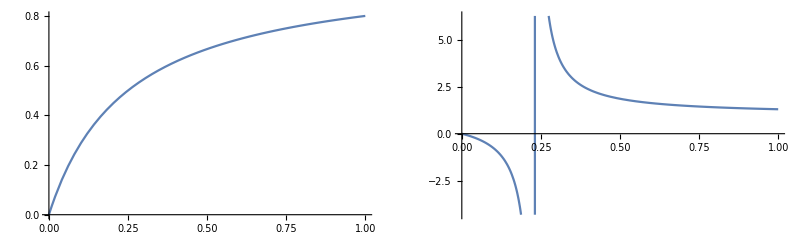

```mathematica
GraphicsRow[{Plot[f[r]/.a-> 0.8,{r, 0,1}],
                         Plot[f[r]/.a-> 1.3,{r, 0,1}]}]
```

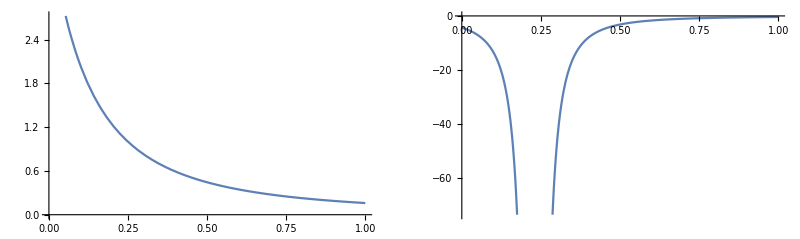

```mathematica
GraphicsRow[{Plot[f'[r]/.a-> 0.8,{r, 0,1}],
                         Plot[f'[r]/.a-> 1.3,{r, 0,1}]}]
```